36.5 cm

20.5 cm

2 cm

15.67 mm | 1 mV
15.9 mm | 2 mV
16. mm | 3 mV
16.07 mm | 4 mV
16.14 mm | 5 mV
16.18 mm | 6 mV
16.25 mm | 7 mV
16.3 mm | 8 mV
16.36 mm | 9 mV
16.39 mm | 10 mV
16.46 mm | 11 mV
16.51 mm | 12 mV
16.56 mm | 13 mV
16.59 mm | 14 mV
16.62 mm | 15 mV
16.65 mm | 16 mV
16.68 mm | 17 mV
16.71 mm | 18 mV
16.73 mm | 19 mV
16.76 mm | 20 mV
16.78 mm | 21 mV
16.82 mm | 22 mV
16.84 mm | 23 mV
16.87 mm | 24 mV
16.89 mm | 25 mV
16.92 mm | 26 mV
16.96 mm | 27 mV
16.99 mm | 28 mV
17.03 mm | 29 mV
17.07 mm | 30 mV
17.11 mm | 31 mV
17.15 mm | 32 mV
17.19 mm | 33 mV
17.23 mm | 34 mV
17.28 mm | 35 mV
17.38 mm | 36 mV
17.51 mm | 37 mV
17.79 mm | 34 mV
17.96 mm | 29 mV
18.11 mm | 24 mV
18.21 mm | 22 mV
18.33 mm | 18 mV
18.42 mm | 14 mV
18.44 mm | 14 mV
18.46 mm | 13 mV
18.54 mm | 11 mV
18.57 mm | 10 mV
18.77 mm | 6 mV
19.07 mm | 2 mV

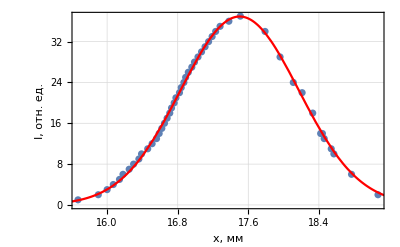

```mathematica
LaserLens=Quantity[36.5,"Centimeters"]
LaserGap=Quantity[20.5,"Centimeters"]
FocusLens = Quantity[2,"Centimeters"]
Experiment1=({{15.67, 1}, {15.90, 2}, {16.0, 3}, {16.07, 4}, {16.14, 5}, {16.18, 6}, {16.25, 7}, {16.30, 8}, {16.36, 9}, {16.39, 10}, {16.46, 11}, {16.51, 12}, {16.56, 13}, {16.59, 14}, {16.62, 15}, {16.65, 16}, {16.68, 17}, {16.71, 18}, {16.73, 19}, {16.76, 20}, {16.78, 21}, {16.82, 22}, {16.84, 23}, {16.87, 24}, {16.89, 25}, {16.92, 26}, {16.96, 27}, {16.99, 28}, {17.03, 29}, {17.07, 30}, {17.11, 31}, {17.15, 32}, {17.19, 33}, {17.23, 34}, {17.28, 35}, {17.38, 36}, {17.51, 37}, {17.79, 34}, {17.96, 29}, {18.11, 24}, {18.21, 22}, {18.33, 18}, {18.42, 14}, {18.44, 14}, {18.46, 13}, {18.54, 11}, {18.57, 10}, {18.77, 6}, {19.07, 2}});
For[i=1,i≤Length[Experiment1],i++,
Experiment1[[i,1]]=Quantity[Experiment1[[i,1]], "Millimeters"];
Experiment1[[i,2]]=Quantity[Experiment1[[i,2]], "Millivolts"];
]
Experiment1//TableForm
GaussianFit=FindFit[QuantityMagnitude[Experiment1[[1;;37]]],{a*E^(-(x-b)^2/(2*c^2)),17≤ b≤ 18},{a,b,c},x];
Show[ListPlot[Experiment1,PlotTheme->"Detailed"],Plot[a*E^(-(x-b)^2/(2*c^2))/.GaussianFit,{x,15,20},PlotStyle->Red],Frame-> True,FrameLabel-> {"x, мм", "I, отн. ед."}]
```

```mathematica
GaussianFit
σ=2 √(2Log[2])*Abs[c]/.GaussianFit
```

{a→36.9233,b→17.5024,c→-0.672486}

1.58358